# Linear Algebra

The Geometry of Linear Equations

#### The Row Picture (2x2) 2x - y = 0 -x + 2y = 3 (2 | -1 | 0 -1 | 2 | 3)(x y)=(0 3) A x⃗ b⃗

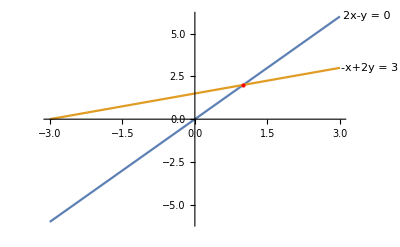
-Graphics-{1,2}

```mathematica
Overlay[{#,{1,2}},Alignment-> {.07,.15}]&@Plot[{2x,(3+x)/2},{x,-3,3},Epilog->{Red,Point[{1,2}]},PlotLabels->Placed[{"2x-y = 0","-x+2y = 3"},After]]
```

### The Column Picture (2x2) x(2 -1)+y(-1 2)=(0 3) 1(2 -1)+2(-1 2)=(0 3)

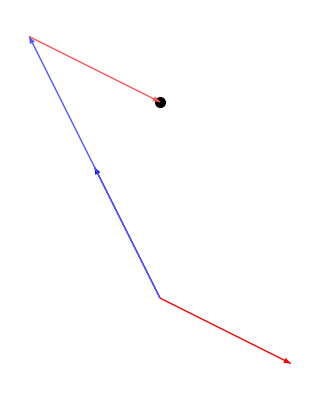

```mathematica
Graphics[{Red,Style[Arrow[{{0,0},{2,-1}}]],Blue,Style[Arrow[{{0,0},{-1,2}}]],Black,PointSize[.02],Point[{0,3}],Lighter[Blue],Style[Arrow[{{0,0},2{-1,2}}]],Lighter[Red],Style[Arrow[{2{-1,2},2{-1,2}+{2,-1}}]]}]
```

### The Row Picture (3x3) 2x - y = 1 -x + 2y - z = -1 -3y + 4z = 5 (2 | -1 | 0 -1 | 2 | -1 0 | -3 | 4)(x y z)=(1 -1 5)

```mathematica
Show[{
Plot3D[{2x-1,(x-1+z)/2,(4z+-5)/3},{x,-3,3},{z,-3,3},PlotStyle->Opacity[.5]],
Graphics3D[{PointSize[.02],Style[Point[{1,2,1}],Red]}]
}]
```

-Graphics3D-

### The Column Picture (3x3) x(2 -1 0)+y(-1 2 -3)+z(0 -1 4)=(1 -1 5) 1(2 -1 0)+1(-1 2 -3)+2(0 -1 4)=(1 -1 5)

```mathematica
Graphics3D[{PointSize[.03],Point[{1,-1,5}],Red,Arrow[{{0,0,0},{2,-1,0}}],Blue,Arrow[{{0,0,0},{-1,2,-3}}],Darker[Green],Arrow[{{0,0,0},{0,-1,4}}],Lighter[Green],Arrow[{{0,0,0},2{0,-1,4}}],Lighter[Blue],Arrow[{2{0,-1,4},2{0,-1,4}+{-1,2,-3}}],Lighter[Red],Arrow[{2{0,-1,4}+{-1,2,-3},2{0,-1,4}+{-1,2,-3}+{2,-1,0}}]},ImageSize->Small]
```

-Graphics3D-

Elimination with Matrices

#### Reduced Matrix x + 2y + z = 2 3x + 8y + z = 12 4y + z = 2 (1 | 2 | 1 3 | 8 | 1 0 | 4 | 1)(x y z)=(2 12 2)→(1 | 2 | 1 | 2 3 | 8 | 1 | 12 0 | 4 | 1 | 2)→^(R_2-3 R_1) (1 | 2 | 1 | 2 0 | 2 | -2 | 6 0 | 4 | 1 | 2)→^(R_3-2 R_2)(1 | 2 | 1 | 2 0 | 2 | -2 | 6 0 | 0 | -3 | -10)→^(R_2+R_3)(1 | 2 | 1 | 2 0 | 1 | 0 | 19/3 0 | 0 | 1 | 10/3)→^(R_1-2 R_2-R_3)(1 | 0 | 0 | 14 0 | 1 | 0 | 19/3 0 | 0 | 1 | 10/3)

```mathematica
Row[{Plot3D[{2-x+-y,12-3x-8y,2-4y},{x,-5,5},{y,-5,5},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small],Style["→",40] ,
Graphics3D[{InfinitePlane[{{14,0,0},{14,14,0},{14,0,14}}],InfinitePlane[{{0,19/3,0},{1,19/3,0},{0,19/3,1}}],InfinitePlane[{{0,0,10/3},{1,0,10/3},{0,1,10/3}}]},BoxRatios->{1, 1, 1},ImageSize->Small]}]
```

-Graphics3D-→-Graphics3D-

#### Vector-Matrix Multiplication (a_1 | a_2 | a_3 b_1 | b_2 | b_3 c_1 | c_2 | c_3)(x y z)=x(a_1 b_1 c_1)+y(a_2 b_2 c_2)+z(a_3 b_3 c_3) (x | y | z)(a_1 | a_2 | a_3 b_1 | b_2 | b_3 c_1 | c_2 | c_3)= x (a_1 | a_2 | a_3) + y(b_1 | b_2 | b_3) + z(c_1 | c_2 | c_3)

#### Row Operation Matrices (1 | 0 | 0 -3 | 1 | 0 0 | 0 | 1)(1 | 2 | 1 3 | 8 | 1 0 | 4 | 1)=(1 | 2 | 1 0 | 2 | -2 0 | 4 | 1)→ (1 | 0 | 0 0 | 1 | 0 0 | -2 | 1)(1 | 2 | 1 0 | 2 | -2 0 | 4 | 1)=(1 | 2 | 1 0 | 2 | -2 0 | 0 | 5) E_21 A E_21A E_32 E_21A E_32 (E_21A) Matrix multiplication is associative, therefore E_32 (E_21 A) = (E_32 E_21)A

#### Permutation Matrices (0 | 1 1 | 0)(a_1 | a_2 b_1 | b_2)=(b_1 | b_2 a_1 | a_2) (a_1 | a_2 b_1 | b_2)(0 | 1 1 | 0)=(a_2 | a_1 b_2 | b_1)

Multiplication and Inverses

#### Multiplication (... | ... | ... A_i1 | A_i2 | A_i3 ... | ... | ...)(... | B_(1j) | ... ... | B_(2j) | ... ... | B_(3j) | ...)=(... | ... | ... ... | C_ij | ... ... | ... | ...); (Row i of A)·(Column j of B) = C_ij (| | | | | | | | | | ... | ... | ...)(| | ... | ... | | ... | ... | | ... | ...)=(| | | | ... | | | | ... | | | | ...); Columns of C are combinations of the columns of A (- | - | - ... | ... | ... ... | ... | ...)(- | - | - - | - | - ... | ... | ...)=(- | - | - - | - | - ... | ... | ...); Rows of C are combinations of the rows of B (a_1 | a_2 b_1 | b_2 c_1 | c_2)(A_1 | A_2 B_1 | B_2)=(a_1 b_1 c_1)(A_1 A_2)+(a_2 b_2 c_2)(B_1 B_2); By Rows and Columns (A_11 | A_12 A_21 | A_22 | B_11 | B_12 B_21 | B_22 C_11 | C_12 C_21 | C_22 | D_11 | D_12 D_21 | D_22)(α_11 | α_12 α_21 | α_22 | β_11 | β_12 β_21 | β_22 γ_11 | γ_12 γ_21 | γ_22 | δ_11 | δ_12 δ_21 | δ_22)=(A | B C | D)(α | β γ | δ)=(Aα+Bγ | Cα+Dγ Aβ+Bδ | Cβ+Dδ); By Blocks

#### Non Invertible Matrices If there is an x⃗≠0 such that Ax⃗= 0, then A is non-invertible (1 | 3 2 | 6)(3 -1)=(0 0)

#### Inverse of a Matrix (Gauss-Jordan) If there is an x⃗≠0 such that Ax⃗= 0, then A is non-invertible (1 | 3 2 | 6)(3 -1)=(0 0) Otherwise: (1 | 3 2 | 7)(a | b c | d)=(1 | 0 0 | 1) (1 | 3 2 | 7)(a c)=(1 0) & (1 | 3 2 | 7)(b d)=(0 1) (1 | 3 2 | 7)(1 | 0 0 | 1)→ (1 | 0 0 | 1)(7 | -3 -2 | 1) A I I A^-1 E[(1 | 3 2 | 7)(1 | 0 0 | 1)]→ (1 | 0 0 | 1)(7 | -3 -2 | 1);E[AI] = IA^-1

Factorizing into A=LU

#### Product of Elimination Matrices (1 | 0 -4 | 1)(2 | 1 8 | 7)=(2 | 1 0 | 3);E_21 A=U (2 | 1 8 | 7)=(1 | 0 4 | 1)(2 | 1 0 | 3); A=E_21^-1 U=LU (No row exchanges)

Transposes, Permutations, Spaces R^n

#### Permutations (General Case for LU Factorization) PA=LU; where P is a permutation matrix P^-1=P^T Transposes A_ij^T=A_ji If A^T=A, then A is symmetric A^T A is always symmetric since (A^T A)^T=A^T A Vector Spaces The first quadrant in R^2 is not a vector space since it’s not closed: (1 2)+(-1)(2 5/2)=(-1 -1/2)

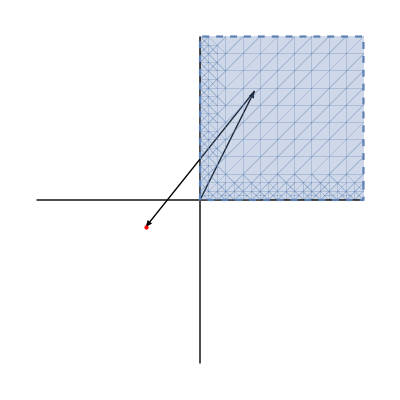

```mathematica
Show[{Graphics[{Line[{{0,3},{0,-3}}],Line[{{-3,0},{3,0}}],Arrow[{{0,0},{1,2}}],Arrow[{{1,2},{-1,-.5}}],Red,Point[{-1,-.5}]}],
RegionPlot[x>0&&y>0,{x,-3,3},{y,-3,3}, BoundaryStyle->Dashed]}]
```

Column Space and Nullspace

#### Column Space For an n×m matrix A, where n ≥ m: A = (a_1 | a_2 | ... b_1 | b_2 | ... c_1 | c_2 | ... ... | ... | ...), the linear combinations of its columns form an m-dimensional subspace in R^n C(A) For any two subspaces S and T: S ∪ T IS NOT a subspace S ∩ T IS a subspace

#### Nullspace For an n×m matrix A, where n ≥ m: all solutions x⃗ to A x⃗ = 0 form an (n – m)-dimensional subspace in R^m called the nullspace

Solving Ax⃗ = 0: Pilot variables and Special Solutions

#### Nullspace Matrix (N) (1 | 2 | 2 | 2 2 | 4 | 6 | 8 3 | 6 | 8 | 10)(x_1 x_2 x_3)=(0 0 0)→(1 | 2 | 0 | -2 0 | 0 | 1 | 2 0 | 0 | 0 | 0)(x_1 x_2 x_3)=(0 0 0) ; # pivots = rank; rank(A) = rank(A^T) R x⃗ = 0 x⃗ = c_1(-(2) 1 -(0) 0)+ c_2(-(-2) 0 -(2) 1); N =(-2 | 2 1 | 0 0 | -2 0 | 1) R = (I | F); then since RN = 0, N = (-F I)

Solving Ax⃗ = b⃗: Row Reduced Form R

#### Finding the Complete Solution 1. Find x_particular: Free variables → 0, solve Ax⃗= b for pivots 2. Find x_nullspace (N) 3. x_complete = x_particular+ cN Example: (1 | 2 | 2 2 | 4 | 6 3 | 6 | 8)(x_1 x_2 x_3)=(3 2 5)→(1 | 2 | 0 0 | 0 | 1 0 | 0 | 0)(x_1 x_2 x_3)=(7 -2 0) x_particular = (7 0 -2) (1 | 2 | 2 2 | 4 | 6 3 | 6 | 8)(x_1 x_2 x_3)=(0 0 0)→(1 | 2 | 0 0 | 0 | 1 0 | 0 | 0)(x_1 x_2 x_3)=(0 0 0) x_nullspace = c (-2 1 0) x_complete = (7 0 -2)+ c (-2 1 0)

```mathematica
Graphics3D[{Arrow[{{-10,0,0},{10,0,0}}],Arrow[{{0,-10,0},{0,10,0}}],Arrow[{{0,0,-10},{0,0,10}}],Red,PointSize[.015],Point[{7,0,-2}],Arrowheads[.02],Arrow[{{0,0,0},{7,0,-2}}],White,InfiniteLine[{7,0,-2},{-2,1,0}]},SphericalRegion->True]
```

-Graphics3D-

#### Four Possibilities For an f×c matrix A , where r = rank(A) ★r = f =c R = [I] → 1 solution (3 | -3 | 1 -1 | 2 | -1 0 | -3 | 4)(x y z)=(2 -1 5)→(1 | 0 | 0 0 | 1 | 0 0 | 0 | 1)(x y z) =(1 1 2)

```mathematica
p2vec3D[ps_]:=If[Length[ps]==1,{{0,0,0},Flatten[ps]},{Total[ps⟦;;-2⟧],Flatten[Total[ps]]}]
Row[{
Show[{Plot3D[{2-3x+3y,1-x+2y,(5+3y)/4},{x,-5,5},{y,-5,5},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True,Mesh->None],Graphics3D[{PointSize[.03],Style[Point[{1,1,2}],Red]}] }],
Style["→",40],
Show[{Graphics3D[{Opacity[.5],InfinitePlane[{{1,0,0},{1,1,0},{1,0,1}}],InfinitePlane[{{0,1,0},{1,1,0},{0,1,1}}],InfinitePlane[{{0,0,2},{1,0,2},{0,1,2}}]},BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True],Graphics3D[{PointSize[.03],Style[Point[{1,1,2}],Red]}] }],
Style["⇔",40],
Graphics3D[{Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],Pink,Arrowheads[.04],Arrow[p2vec3D[#]&/@Drop[Permutations[{{3,-1,0},{-3,2,-3},{1,-1,4}}{1,1,2},3],1]],Red,PointSize[.03],Point[{2,-1,5}]},ImageSize-> Small,SphericalRegion->True],
Style["→",40],
Graphics3D[{Arrow[{{-3,0,0},{3,0,0}}],Arrow[{{0,-3,0},{0,3,0}}],Arrow[{{0,0,-3},{0,0,3}}],Pink,Arrowheads[.03],Arrow[p2vec3D[#]&/@Drop[Permutations[{{1,0,0},{0,1,0},{0,0,1}}{1,1,2},3],1]],Red,Point[{1,1,2}]},ImageSize->Small,SphericalRegion->True]
}]
```

-Graphics3D-→-Graphics3D-⇔-Graphics3D-→-Graphics3D-

#### ★r = c < f R = [I 0] → 0 or 1 solution (2 | -1 | 0 -3 | -2 | 0 1 | -2 | 0)(x y z)=(10 -1 11)→(1 | 0 | 0 0 | 1 | 0 0 | 0 | 0)(x y z) =(3 -4 0)→(1 | 0 0 | 1)(x y) =(3 -4)

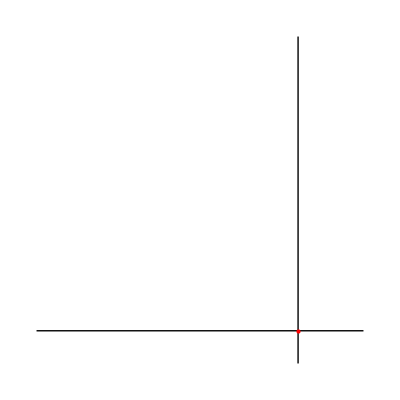
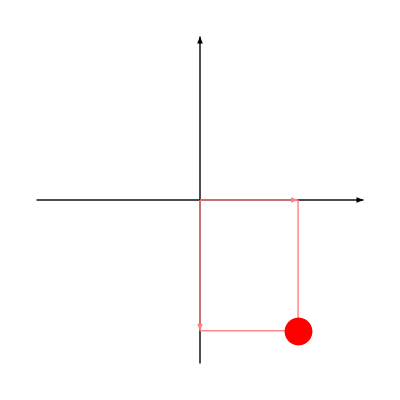
-Graphics3D-→-Graphics3D-→-Graphics-⇔-Graphics3D-→-Graphics3D-→-Graphics-

```mathematica
p2vec3D[ps_]:=If[Length[ps]==1,{{0,0,0},Flatten[ps]},{Total[ps⟦;;-2⟧],Flatten[Total[ps]]}]
Row[{
Show[{Plot3D[{2x-10,(1-3x)/2,(x-11)/2},{z,-5,5},{x,-5,5},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True,Mesh->None],ParametricPlot3D[{z,3,-4},{z,-5,5},PlotStyle->Red] }],
Style["→",40],
Show[{Graphics3D[{Opacity[.5],InfinitePlane[{{3,0,0},{3,1,0},{3,0,1}}],InfinitePlane[{{0,-4,0},{1,-4,0},{0,-4,1}}]},BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True],ParametricPlot3D[{3,-4,z},{z,-5,5},PlotStyle->Red] }],
Style["→",40],
Graphics[{Line[{{3,-5},{3,5}}],Line[{{-5,-4},{5,-4}}],Red,Point[{3,-4}]}],
Style["⇔",40],
Graphics3D[{Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],Pink,Arrowheads[.05],Arrow[p2vec3D[#]&/@Drop[Permutations[{{2,-3,1},{-1,-2,-2},{0,0,0}}{3,-4,0},3],1]],Red,PointSize[.03],Point[{10,-1,11}]},ImageSize-> Small,SphericalRegion->True],Style["→",40],
Graphics3D[{Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],Pink,Arrowheads[.05],Arrow[p2vec3D[#]&/@Drop[Permutations[{{1,0,0},{0,1,0},{0,0,0}}{3,-4,0},3],1]],Red,PointSize[.03],Point[{3,-4,0}]},ImageSize->Small,SphericalRegion->True],
Style["→",40],
Graphics[{Arrowheads[.1],Arrow[{{-5,0},{5,0}}],Arrow[{{0,-5},{0,5}}],Pink,Arrow[{{0,0},{3,0}}],Arrow[{{0,0},{0,-4}}],Arrow[{{3,0},{3,-4}}],Arrow[{{0,-4},{3,-4}}],Red,PointSize[.05],Point[{3,-4}]}]
}]
```

#### → 1 or 0 solutions (2 | -1 | 0 -3 | -2 | 0 1 | -2 | 0)(x y z)=(5 -1 15)→(1 | 0 | 0 0 | 1 | 0 0 | 0 | 0)(x y z) =(0 0 1)

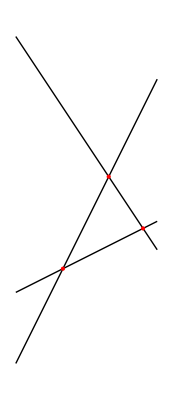
-Graphics3D-→-Graphics-⇔-Graphics3D-→-Graphics3D-

```mathematica
p2vec3D[ps_]:=If[Length[ps]==1,{{0,0,0},Flatten[ps]},{Total[ps⟦;;-2⟧],Flatten[Total[ps]]}]
Row[{
Show[{Plot3D[{2x-5,(1-3x)/2,(x-15)/2},{z,-5,5},{x,-5,5},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True,Mesh->None],ParametricPlot3D[{z,11/7,-13/7},{z,-5,5},PlotStyle->Red] ,ParametricPlot3D[{z,-5/3,-25/3},{z,-5,5},PlotStyle->Red],ParametricPlot3D[{z,4,-11/2},{z,-5,5},PlotStyle->Red]}],
Style["→",40],
Graphics[{Line[{{-5,-15},{5,5}}],Line[{{-5,8},{5,-7}}],Line[{{-5,-10},{5,-5}}],Red,Point[{{11/7,-13/7},{-5/3,-25/3},{4,-11/2}}]}],
Style["⇔",40],
Graphics3D[{Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],Pink,Arrowheads[.04],Arrow[p2vec3D[#]&/@Drop[Permutations[{{2,-3,1},{-1,-2,-2},{0,0,0}}{2,-2,0},3],1]],Red,PointSize[.03],Point[{2,-1,5}]},ImageSize-> Small,SphericalRegion->True],Style["→",40],
Graphics3D[{Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],Pink,Arrowheads[.04],Arrow[p2vec3D[#]&/@Drop[Permutations[{{1,0,0},{0,1,0},{0,0,0}}{4,-4,0},3],1]],Red,PointSize[.025],Point[{2,-1,5}]},ImageSize->Small,SphericalRegion->True]
}]
```

#### ★r = f < c R = [I | F] (2 | -3 | -4 -3 | -2 | -7)(x y z)=(18 -1)→(1 | 0 | 1 0 | 1 | 2)(x y z) =(3 -4) → ∞ solutions

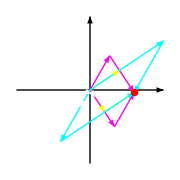
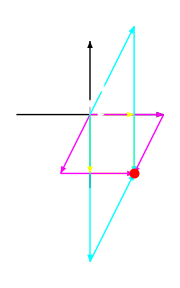
-Graphics3D-→-Graphics3D-⇔-Graphics-→-Graphics-

```mathematica
Row[{
Show[{Plot3D[{(2x-3y-18)/4,(-3x-2y+1)/7},{x,-5,5},{y,-10,0},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True,Mesh->None],ParametricPlot3D[{3-z,-4-2z,z},{z,-2,3},PlotStyle->Red]}],
Style["→",40],
Show[{Plot3D[{3-x,(-4-y)/2},{x,-5,5},{y,-10,0},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True,Mesh->None],ParametricPlot3D[{3-z,-4-2z,z},{z,-2,3},PlotStyle->Red]}],
Style["⇔",40],
Graphics[{Arrowheads[.08],Arrow[{{0,-30},{0,30}}],Arrow[{{-30,0},{30,0}}],
Arrowheads[.05],
White,Arrow[{{0,0},{2,-3}}],Arrow[{{0,0},{-3,-2}}],Arrow[{{0,0},{-4,-7}}],
Yellow,Arrow[3{{0,0},{2,-3}}],Arrow[{3{2,-3},{18,-1}}],Arrow[-4{{0,0},{-3,-2}}],Arrow[{-4{-3,-2},{18,-1}}],
Magenta,Arrow[5{{0,0},{2,-3}}],Arrow[{5{2,-3},{18,-1}}],Arrow[-2{{0,0},{-4,-7}}],Arrow[{-2{-4,-7},{18,-1}}],
Cyan,Arrow[-10{{0,0},{-3,-2}}],Arrow[{-10{-3,-2},{18,-1}}],Arrow[3{{0,0},{-4,-7}}],Arrow[{3{-4,-7},{18,-1}}],
Red,PointSize[.03],Point[{18,-1}]},ImageSize->Small],
Style["→",40],,
Graphics[{Arrowheads[.08],Arrow[{{0,-5},{0,5}}],Arrow[{{-5,0},{5,0}}],
Arrowheads[.06],
White,Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{0,1}}],Arrow[{{0,0},{1,2}}],
Yellow,Arrow[{{0,0},{3,0}}],Arrow[{{3,0},{3,-4}}],Arrow[{{0,0},{0,-4}}],Arrow[{{0,-4},{3,-4}}],
Magenta,Arrow[{{0,0},{5,0}}],Arrow[{{5,0},{3,-4}}],Arrow[-2{{0,0},{1,2}}],Arrow[{-2{1,2},{3,-4}}],
Cyan,Arrow[{{0,0},{0,-10}}],Arrow[{{0,-10},{3,-4}}],Arrow[3{{0,0},{1,2}}],Arrow[{3{1,2},{3,-4}}],
Red,PointSize[.04],Point[{3,-4}]},
ImageSize->Small]
}]
```

#### ★r < f, r < c R = [I | F 0 | 0] (3 | -1 | 7 -2 | -2 | -2 1 | -2 | 4)(x y z)=(13 2 11)→(1 | 0 | 2 0 | 1 | -1 0 | 0 | 0)(x y z) =(3 -4 0) → 0 or ∞ solutions

```mathematica
p2vec3D[ps_]:=If[Length[ps]==1,{{0,0,0},Flatten[ps]},{Total[ps⟦;;-2⟧],Flatten[Total[ps]]}]
Row[{
Show[{Plot3D[{(13-3x+y)/7,x-y-1,(11-x+2y)/4},{x,-5,5},{y,-5,5},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True,Mesh->None],
ParametricPlot3D[{3-2z,z-4,z},{z,-1,4},PlotStyle->Red]}],
Style["→",40],
Show[{Plot3D[{(3-x)/2,y+4},{x,-5,5},{y,-5,5},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True,Mesh->None],ParametricPlot3D[{3-2z,z-4,z},{z,-1,4},PlotStyle->Red]}],
Style["⇔",40],
Show[{
Graphics3D[{Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],Pink,Arrowheads[.02],Arrow[p2vec3D[#]&/@Drop[Permutations[{{3,-2,1},{-1,-2,-2},{7,-2,4}}{1,1,1},3],1]]},ImageSize-> Small,SphericalRegion->True],ParametricPlot3D[{3-2z,z-4,z},{z,-1,4},PlotStyle->Red]}],
Style["→",40],
Show[{
Graphics3D[{Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],Pink,Arrowheads[.02],Arrow[p2vec3D[#]&/@Drop[Permutations[{{1,0,0},{0,1,0},{2,-1,0}}{3,-4,0},3],1]]},ImageSize->Small,SphericalRegion->True],
ParametricPlot3D[{3-2z,z-4,z},{z,-1,4},PlotStyle->Red]}]
}]
```

-Graphics3D-→-Graphics3D-⇔-Graphics3D-→-Graphics3D-

#### (3 | -1 | 7 -2 | -2 | -2 1 | -2 | 4)(x y z)=(13 2 12)→(1 | 0 | 2 0 | 1 | -1 0 | 0 | 0)(x y z) =(0 0 1) → ∞ or 0 solutions

```mathematica
p2vec3D[ps_]:=If[Length[ps]==1,{{0,0,0},Flatten[ps]},{Total[ps⟦;;-2⟧],Flatten[Total[ps]]}]
Row[{
Show[{Plot3D[{(13-3x+y)/7,x-y-1,(12-x+2y)/4},{x,-5,5},{y,-5,5},PlotStyle->Opacity[.5],BoxRatios->{1, 1, 1},ImageSize->Small,SphericalRegion->True,Mesh->None]}],
Style["⇔",40],
Graphics3D[{Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],Pink,Arrowheads[.02],Arrow[p2vec3D[#]&/@Drop[Permutations[{{3,-2,1},{-1,-2,-2},{7,-2,4}}{-1,1,1},3],1]],Red,Point[{2,-1,5}]},ImageSize-> Small,SphericalRegion->True]
}]
```

-Graphics3D-⇔-Graphics3D-

Independence, Basis and Dimension

#### The subspace that the column vectors of matrix A span is C(A). rank(A) = dim(C(A)) For an n-dimensional subspace, n vectors suffice to form a basis as long as they are independent. n = dim(C(A)) + dim(N(A))

The Four Fundamental Subspaces

#### Let A be an m x n matrix, then: Column Space: Shorthand: C(A) Basis: pivot columns Dimension: rank(A) Lives in: ℝ^m Left Null Space: Shorthand: N(A^T) Basis: last m-r rows of E Dimension: m – rank(A) Lives in: ℝ^m Row Space: Shorthand: C(A^T) Basis: first r rows of R Dimension: rank(A) Lives in: ℝ^n Null Space: Shorthand: N(A) Basis: special solutions Dimension: n – rank(A) Lives in: ℝ^n Row operations preserve the row-space Left nullspace: Aᵀy = 0 → yᵀA = 0 rref[A_mxn | I_mxm]=[R_mxn | E_mxm]→E_mxm[A_mxn | I_mxm]=[R_mxn | E_mxm] Then the last m-r rows of E are N(Aᵀ) If m = n, E = A^-1.

Matrix Spaces; Rank 1; Small World Graphs

#### Let M be the vector space of all 3x3 matrices. A basis for M would be: (1 | 0 | 0 0 | 0 | 0 0 | 0 | 0) + (0 | 1 | 0 0 | 0 | 0 0 | 0 | 0) + (0 | 0 | 1 0 | 0 | 0 0 | 0 | 0) + ... + (0 | 0 | 0 0 | 0 | 0 0 | 0 | 1), therefore dim(M) = 9 Let S be the vector space of all symmetric 3x3 matrices, then dim(S) = 6 Let U be the vector space of all upper triangular 3x3 matrices, then dim(U) = 6 S ∩ U is then the vector subspace of M of diagonal matrices and dim(S∩U) = 3 S ∪ U is not a subspace of M. S + U = M. dim(S) + dim(U) = dim(S ∩ U) + dim(S + U) = 12 Let A and B be any two subspaces, then dim(A) + dim(B) = dim(A ∩ B) + dim(A + B) Every rank 1 matrix A has the form: A = u vᵀ = [... | ...][... ...] Every matrix of rank r can be decomposed into r rank 1 matrices. Subsets of a given rank are NOT subspaces. Example: In ℝ^4: S = (s_1 s_2 s_3 s_4) such that s_1+s_2+s_3+s_4=0 Can be seen as the nullspace of A = [1 | 1 | 1 | 1] rank(A) = 1, dim(N(A)) = dim(S) = 3 A basis for S would be: (-1 1 0 0) , (-1 0 1 0), (-1 0 0 1) dim(C(Aᵀ)) = 1 C(A) = ℝ^1, therefore dim(N(Aᵀ)) = 0 since m = 1 N(Aᵀ) = {0}

Graphs, Networks, Incidence Matrices

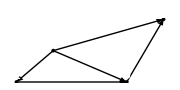

```mathematica
p1 = {1,1};p2 ={0,0};p3 ={3,0};p4 = {4,2};
Graphics[{PointSize[.015],Arrowheads[.04],Point[{p1,p2,p3,p4}],Arrow[{{p1,p2},{p1,p3},{p1,p4},{p2,p3},{p3,p4}}],
Inset[Style["1",15,White],p1,{Center,Bottom}],Inset[Style["2",15,White],p2,{Center,Bottom}],Inset[Style["3",15,White],p3,{Center,Bottom}],Inset[Style["4",15,White],p4,{Center,Bottom}]
},ImageSize->Small]
```

### Incidence Matrix n | o | d | e | s A = (-1 | 1 | 0 | 0 0 | -1 | 1 | 0 -1 | 0 | 1 | 0 -1 | 0 | 0 | 1 0 | 0 | -1 | 1) e d g e s N(A) : Ax = (x_2-x_1 x_3-x_2 x_3-x_1 x_4-x_1 x_4-x_3)=(0 0 0 0 0) → c (1 1 1 1 1) Grounding a node makes its column all 0s N(Aᵀ): Aᵀy = 0 ← KCL e | d | g | e | s Aᵀ = (-1 | 0 | -1 | -1 | 0 1 | -1 | 0 | 0 | 0 0 | 1 | 1 | 0 | -1 0 | 0 | 0 | 1 | 1)(y_1 y_2 y_3 y_4 y_5) n o d e s

### Basis from the loops: {(1 1 -1 0 0), (0 0 1 -1 1)} Dependencies in the columns come from loops. Three independent vectors will form a tree. Euler’s Formula: #nodes – #edges ++ #loops = 1 potentials (Ax) → currents(CAx) → KCL(AᵀCAx) For an external source f: f = AᵀCAx

Quiz 1 Review

#### N(CD) = N(D), if C is invertible. The row-space and the nullspace are perpendicular and their intersection is the zero vector.

Orthogonal Vectors  and Subspaces

#### ||x(||)^2+||y(||)^2=||x+y(||)^2 → xᵀx+yᵀy=(x+y)ᵀ(x+y) → xᵀx+yᵀy=xᵀx+yᵀy+2xᵀy → 0=xᵀy x and y are orthogonal if: xᵀy=0 A subspace S is orthogonal to a subspace T if: ∀ s ∈ S and t ∈ T, s ⊥ t. C(Aᵀ) ⊥ N(A) since: (row 1 row 2 ... row m)(x_1 x_2 ... x_n) = (0 0 0 0) → (c_1 row1+c_2 row2+...)ᵀx=0 Similarly, C(A) ⊥ N(Aᵀ) Row-space and nullspace are orthogonal complements in ℝ^n since the nullspace contains every vectors perpendicular to the row-space. A x = (1 | 2 | 5) (x_1 x_2 x_3) = ( 0 ) Row-space: c_1 (1 2 5) Nullspace: x+2y+5z=0

```mathematica
Show[{
Plot3D[(-x-2y)/5,{x,-5,5},{y,-5,5},ImageSize->{300},SphericalRegion->True,Mesh->None,PlotStyle->{Opacity[.5],Black},BoxRatios->Automatic],Graphics3D[{Thick,White,InfiniteLine[{{0,0,0},{1,2,5}}]}]
}]
```

-Graphics3D-

#### AᵀA: ·Square ·Symmetric ·N(AᵀA) = N(A) ·rank(AᵀA) = rank(A) ·AᵀA is invertible if N(A) = { 0 }

Projections onto Subspaces

{7/5,7/10}

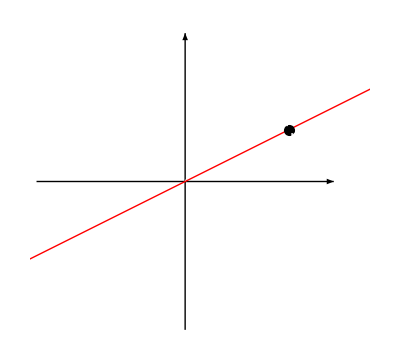

```mathematica
proj[a_,b_]:=Flatten[((a.aᵀ)/((aᵀ.a )⟦1,1⟧)).b]
a={1,1/2};
b={1,3/2};
p=proj[List/@a,List/@b]
Graphics[{Arrow[{{-2,0},{2,0}}],Arrow[{{0,-2},{0,2}}],PointSize[.02],White,Arrow[{{0,0},b}],Inset[Style["b",15,White],b,{Center,Bottom}],Red,Thick,InfiniteLine[{{0,0},a}],Black,Point[p],Inset[Style["p",15,White],p,{Left,Top}],Dashed,White,Line[{b,p}],Inset[Style["e",15,White],p+{-.1,.6},{Left,Top}],Inset[Style["a",15,White],p+{1,.8},{Left,Top}]},ImageSize->{300}]
```

#### p=xa e=b-p aᵀe=aᵀ(b-p)=aᵀ(b-xa)=0 x=aᵀb/aᵀa→ p =(a aᵀ)/aᵀa b=P b P is the projection matrix onto a C(P) = c a, where c is a constant. Pᵀ=P P^2=P Solve A x̂=Pb

```mathematica
project[A_,b_]:=Flatten[A.Inverse[Aᵀ.A].Aᵀ.b]
A={{1,0,1/5},{0,1,1/5}}ᵀ;
b={1,-3,2};
p = project[A,List/@b];
Show[{
Graphics3D[{Arrow[{{0,0,0},2{1,0,1/5}}],Arrow[{{0,0,0},2{0,1,1/5}}],Thick,Red,Arrow[{{0,0,0},b}],PointSize[.02],Point[p],White,Arrow[{{0,0,0},p}],Dashed,Line[{b,p}],Inset[Style["a_1",15],2{1,0,1/5},{Center,Bottom}],Inset[Style["a_2",15],2{0,1,1/5},{Center,Bottom}],Inset[Style["e",15],.5(b+p)+.05p,{Left,Center}],Inset[Style["b",15],.5b+.05(b-p),{Left,Bottom}],Inset[Style["e",15],.5(b+p)+.05p,{Left,Center}],Inset[Style["P",15],.5p+.05p,{Center,Top}]}],
Plot3D[{(x+y)/5},{x,-3,3},{y,-3,3},Mesh->None,SphericalRegion->True,ImageSize->{300},PlotStyle->{Opacity[.5],Black},BoxRatios->Automatic]
}]
```

-Graphics3D-

### A = (a_1 | a_2) plane = span(a_(1,)a_2)=C(A) e⊥plane (a_1 ᵀ a_2 ᵀ) (e)=(0 0) → (Aᵀ) (e)=(0) e∈N(Aᵀ) → e⊥C(A) e=b-P =b-A x̂ Aᵀ(e)=Aᵀ(b-A x̂)=0 →AᵀA x̂=Aᵀb→x̂=(AᵀA)^-1 Aᵀ b P=A x̂=A (AᵀA)^-1 Aᵀ b

Projection Matrices and Least Squares

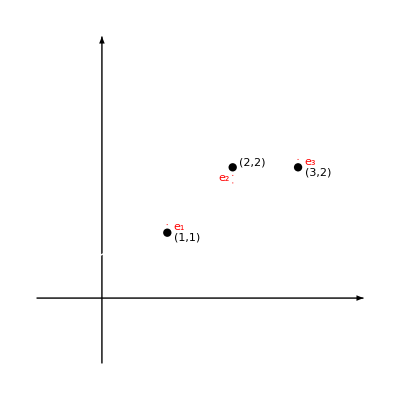

```mathematica
Graphics[{White,InfiniteLine[{{0,2/3},{1,7/6}}],
Dotted,Red,Line[{{1,1},{1,2/3+1/2}}],Line[{{2,2},{2,2/3+1}}],Line[{{3,2},{3,2/3+3/2}}],
Inset["e_1",.5*({1.2,1}+{1,7/6}),{Left,Center}],Inset["e_2",.5*({1.9,2}+{2,10/6}),{Right,Center}],Inset["e_3",.5*({3.2,2}+{3,13/6}),{Left,Center}],
Dashing[None],Black,Arrow[{{{-1,0},{4,0}},{{0,-1},{0,4}}}],PointSize[.015],Point[{{1,1},{2,2},{3,2}}],
Inset["(1,1)",{1.1,1},{Left,Top}],Inset["(2,2)",{2.1,2},{Left,Bottom}],Inset["(3,2)",{3.1,2},{Left,Top}]}]
```

#### We need to fit the line (y = C + Dt) closest to the points. Our system is: C+D=1 C+2D=2 C+3D=2 → (1 | 1 1 | 2 1 | 3)(C D)= (1 2 2) Ought to minimize: ||error(||)^2 = ||Ax – b(||)^2 We find the normal equations: AᵀA x̂=Aᵀb: (1 | 1 | 1 1 | 2 | 3)(1 | 1 1 | 2 1 | 3)(C D)= (1 | 1 | 1 1 | 2 | 3)(1 2 2) 3C+6D 6C+14D= =5 11→ C=2/3 D=1/2 *We can also obtain the normal equations through calculus: ∂_C [(C+D-1)^2+(C+2D-2)^2+(C+3D-2)^2]=6C+12D-10 ∂_D [(C+D-1)^2+(C+2D-2)^2+(C+3D-2)^2]=12C+28D-22 Therefore, the best line is: 2/3+1/2 t b = p + e (1 2 2)=(7/6 10/6 13/6)+(-1/6 2/6 -1/6) N(Aᵀ) ∋ e ⊥ C(A) If A has independent columns, then AᵀA is invertible: Proof: For AᵀA to be invertible, x must be the zero vector in: (Aᵀ A) x = 0 If we multiply by xᵀ on the left we can have insight: (xᵀAᵀ) (A x) = (A x)ᵀ (A x) = ||(A x)(||)^2 = 0 → (A x) = 0 If A has independent columns, then x must be the zero vector.

Orthogonal Matrices and Gram-Schmidt

#### Orthonormal vectors: q_i ᵀ q_j={0, if i ≠ j 1, if i = j Q=(q_1 | ... | q_n) Q must be square: QᵀQ=I→Qᵀ=Q^(–1) Hadamard: 1/2(1 | 1 | 1 | 1 1 | -1 | 1 | -1 1 | 1 | -1 | -1 1 | -1 | -1 | 1) Projecting onto Q: P=Q (QᵀQ)^-1 Qᵀ=Q Qᵀ Then: Qᵀ Q x̂=x̂=Qᵀb (x̂)_i=qᵀ_i b Gram-Schmidt:

```mathematica
project[A_,b_]:=Flatten[A.Inverse[Aᵀ.A].Aᵀ.b]
a={1,1,1};b={1,0,2};c={1,2,3};
A=a;B=b-(pAb=project[List/@A,List/@b]);vC=c-(pAc=project[List/@A,List/@c])-(pBc=project[List/@B,List/@c]);
q1 = A/(Norm@A);q2 = B/(Norm@B); q3 = vC/(Norm@vC);
Row[{
Graphics3D[{Arrowheads[.02],Arrow[{{-3,0,0},{3,0,0}}],Arrow[{{0,-3,0},{0,3,0}}],Arrow[{{0,0,-3},{0,0,3}}],
Arrowheads[.03],
Red, Arrow[{{{0,0,0},b},{{0,0,0},c}}],
Purple,Arrow[{{0,0,0},a}]
},ImageSize->{250},SphericalRegion->True],
Style["→",40],
Graphics3D[{Arrowheads[.02],Arrow[{{-3,0,0},{3,0,0}}],Arrow[{{0,-3,0},{0,3,0}}],Arrow[{{0,0,-3},{0,0,3}}],
Arrowheads[.03],Red,Arrow[{{0,0,0},b}],Arrow[{{0,0,0},c}],
Blue, Arrow[{{{0,0,0},A},{{0,0,0},B}}],
White,Dashed,Line[{b,pAb}],Blue,Arrowheads[.02],Arrow[{b,B}]
},ImageSize->{250},SphericalRegion->True],
Style["→",40],
Graphics3D[{Arrowheads[.02],Arrow[{{-3,0,0},{3,0,0}}],Arrow[{{0,-3,0},{0,3,0}}],Arrow[{{0,0,-3},{0,0,3}}],
Arrowheads[.03],Red,Arrow[{{0,0,0},c}],
Blue, Arrow[{{{0,0,0},A},{{0,0,0},B},{{0,0,0},vC}}],
White,Dashed,Line[{{c,pAc},{c,pBc}}],Blue,Arrowheads[.02],Arrow[{c,vC}]
},ImageSize->{250},SphericalRegion->True],
Style["→",40],
Graphics3D[{Arrowheads[.02],Arrow[{{-3,0,0},{3,0,0}}],Arrow[{{0,-3,0},{0,3,0}}],Arrow[{{0,0,-3},{0,0,3}}],
Arrowheads[.03],
White, Arrow[{{{0,0,0},q1},{{0,0,0},q2},{{0,0,0},q3}}]
},ImageSize->{250},SphericalRegion->True]
}]
```

-Graphics3D-→-Graphics3D-→-Graphics3D-→-Graphics3D-

#### Given the vectors, a,b and c → obtain q_1,q_2,q_3 q_1=e_a/(||e_a||), q_2=e_b/(||e_b||), q_3=e_c/(||e_c||) we set P_a = a We remove from b the projection of itself onto e_a to obtain e_b: e_b=b-e_a (e_a ᵀ e_a)^-1 e_a ᵀ b or b-((e_a ᵀ b)/(e_a ᵀ e_a))e_a We check orthogonality: e_a ᵀ e_b=e_a ᵀ(b-e_a (e_a ᵀ e_a)^-1 e_a ᵀ b)=e_a ᵀb - [(e_a ᵀ e_a) (e_a ᵀ e_a)^-1]e_a ᵀb=0 To obtain e_c: e_c=c-(e_a(e_a ᵀ e_a))^-1 e_a ᵀ c-(e_b(e_b ᵀ e_b))^-1 e_b ᵀ c For given vectors a and b: (a | b)=(q_1 | q_2)(aᵀ q_1 | bᵀ q_1 aᵀ q_2 | bᵀ q_2) → A=Q R R is upper triangular.

Properties of Determinants

#### 1) det( I ) = | I | = 1 2) Row permutations change its sign if the number of permutations is odd 3) a. |t a | t b c | d|=t|a | b c | d| 3) b. |a+a' | b+b' c | d|=|a | b c | d|+|a' | b' c | d| INDEPENDENT row linearity: det(A+b)≠det(A) + det(B) Emergent properties: ⋆ It is invariant under the sum of C×row_i from row_k: |a | b c+C a | d+C b|=|a | b c | d|+|a | b C a | C b|=|a | b c | d|+C|a | b a | b|=|a | b c | d| ⋆ For an upper diagonal matrix U, det(U) = |(d_1 | ... | ... | ... 0 | d_2 | ... | ... 0 | 0 | ... | ... 0 | 0 | 0 | d_n)|=d_1×d_2×d_3×...×d_n|(1 | ... | ... | ... 0 | 1 | ... | ... 0 | 0 | ... | ... 0 | 0 | 0 | 1)|=d_1×d_2×d_3×...×d_n **without row exchanges ⋆ det(A)=0⇔A is singular ⋆ det(A B) = det(A) det(B) ⋆ det(2A) = 2^n det(A) ⋆ det(A) = det(Aᵀ)

Determinant Formulas and Cofactors

#### |a | b c | d|=|a | 0 c | 0|+|a | 0 0 | d|+|0 | b 0 | d|+|0 | b c | 0|=a d-b c |(a_11 | a_12 | a_13 a_21 | a_22 | a_23 a_31 | a_32 | a_33)|=|(a_11 | 0 | 0 0 | a_22 | 0 0 | 0 | a_33)|+|(0 | a_12 | 0 0 | 0 | a_23 a_31 | 0 | 0)|+|(0 | 0 | a_13 a_21 | 0 | 0 0 | a_32 | 0)|+|(a_11 | 0 | 0 0 | 0 | a_23 0 | a_32 | 0)|+|(0 | a_12 | 0 a_21 | 0 | 0 0 | 0 | a_33)|+|(0 | 0 | a_13 0 | a_22 | 0 a_31 | 0 | 0)| =a_11 a_22 a_33|(1 | 0 | 0 0 | 1 | 0 0 | 0 | 1)|+ a_12 a_23 a_31|(0 | 1 | 0 0 | 0 | 1 1 | 0 | 0)|+ a_13 a_21 a_32|(0 | 0 | 1 1 | 0 | 0 0 | 1 | 0)|+ a_11 a_23 a_32|(1 | 0 | 0 0 | 0 | 1 0 | 1 | 0)|+ a_12 a_21 a_33|(0 | 1 | 0 1 | 0 | 0 0 | 0 | 1)|+ a_13 a_22 a_31|(0 | 0 | 1 0 | 1 | 0 1 | 0 | 0)| =a_11 a_22 a_33+ a_12 a_23 a_31 + a_13 a_21 a_32 - a_11 a_23 a_32 - a_12 a_21 a_33 - a_13 a_22 a_31 For an n×n matrix, the determinant has n! terms. Cofactors We factorize the formula above: a_11(a_22 a_33- a_23 a_32)+ a_12(a_23 a_31- a_21 a_33) + a_13(a_21 a_32 - a_22 a_31) =|(a_11 | 0 | 0 0 | a_22 | a_23 0 | a_32 | a_33)|-|(0 | a_12 | 0 a_21 | 0 | a_23 a_31 | 0 | a_33)|+|(0 | 0 | a_13 a_21 | a_22 | 0 a_31 | a_32 | 0)| =a_11|(a_22 | a_23 a_32 | a_33)|- a_12|(a_21 | a_23 a_31 | a_33)|+ a_13|(a_21 | a_22 a_31 | a_32)| We have a minus sign if i+j is odd

Cramer’s Rule, Inverse Matrix, and Volume

#### A^-1=Cᵀ/(det A)<->ACᵀ=(det A)I Cramer’s Rule x=Cᵀb/(det A)→x_j=(det B_j)/(det A) B_j=det (a_11 | ... | b_1 | ... | a_(1n) a_21 | ... | b_2 | ... | a_(2n) ... | ... | ... | ... | ... a_n1 | ... | b_n | ... | a_nn) In ℝ^3, the determinant can be seen as the volume of the parallelepiped created by the the row vectors of the matrix A=(3 | 1 | 0 0 | 2 | 1 1 | 0 | 3)

```mathematica
p2vec3D[ps_]:=If[Length[ps]==1,{{0,0,0},Flatten[ps]},{Total[ps⟦;;-2⟧],Flatten[Total[ps]]}]
A = {{3, 1, 0}, {0, 2, 1}, {1, 0, 3}};
Row[{
Show[{
Graphics3D[{Arrow[4{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-1},{0,0,1}}}],Thick,White,Arrowheads[.03],Arrow[p2vec3D[#]&/@Drop[Permutations[{A⟦All,1⟧,A⟦All,2⟧,A⟦All,3⟧}{1,1,1},3],1]],Red,
Arrow[{{0,0,0},A⟦All,1⟧}],Arrow[{{0,0,0},A⟦All,2⟧}],Arrow[{{0,0,0},A⟦All,3⟧}]
},ImageSize-> 300,SphericalRegion->True],
Graphics3D[{Black,Opacity[.3],𝔸=Parallelepiped[{0,0,0},Aᵀ]}]
}],
Column[{
Style[StringForm["Det(A) = ``",Det[A]],20,FontFamily->"Bahnschrift Light"],,,
Style[StringForm["Volume(A) = ``",Volume[𝔸]],20,FontFamily->"Bahnschrift Light"]
}]
}]
```

-Graphics3D-Det(A) = 19


Volume(A) = 19

#### All the properties of the determinant can be deduced from how matrix operations affect the volume of this parallelepiped

Eigenvalues and Eigenvectors

### For A x = λ x, λ is the eigenvalue, and x is its corresponding eigenvector. (A - λ I)x=0→det(A-λI)=0 n×n matrices have n eigenvalues The sum of the eigenvalues of A = trace of A The product of the eigenvalues of A = det(A) Example: A=(3 | 1 1 | 3)→det (A-λI)=λ^2- 6 λ + 8→λ_1=4, λ_2=2 λ_1=4: (A-4I)x_1=(-1 | 1 1 | -1)x_1=0→x_1=(1 1) λ_2=2: (A-2I)x_2=(1 | 1 1 | 1)x_2=0→x_2=(1 -1)

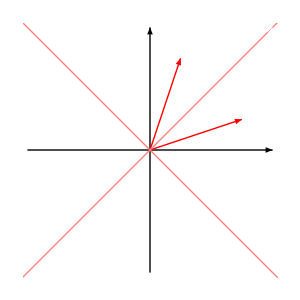

```mathematica
A={{3, 1}, {1, 3}};
Graphics[{Arrow[4{{{-1,0},{1,0}},{{0,-1},{0,1}}}],Red,Arrow[{{{0,0},A⟦All,1⟧},{{0,0},A⟦All,2⟧}}],White, Arrow[{{A⟦All,1⟧,{4,4}},{A⟦All,2⟧,{4,4}}}],Pink,InfiniteLine[#]&/@{{{0,0},{1,1}},{{0,0},{1,-1}}}},ImageSize->300]
```

### In ℝ^3: A=(-3 | 2 | 2 2 | 3 | -1 2 | -1 | 3)

```mathematica
p2vec3D[ps_]:=If[Length[ps]==1,{{0,0,0},Flatten[ps]},{Total[ps⟦;;-2⟧],Flatten[Total[ps]]}]
A = {{-3, 2, 2}, {2, 3, -1}, {2, -1, 3}};
ei = Join[{Eigenvectors[A]},{Eigenvectors[A].A}]ᵀ;
eival = Eigenvalues@A
Show[{
Graphics3D[{Arrow[Max@eival{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-1},{0,0,1}}}],Thick,White,Arrowheads[.03],Arrow[p2vec3D[#]&/@Drop[Permutations[{A⟦All,1⟧,A⟦All,2⟧,A⟦All,3⟧}{1,1,1},3],1]],Red,
Arrow[{{0,0,0},A⟦All,1⟧}],Arrow[{{0,0,0},A⟦All,2⟧}],Arrow[{{0,0,0},A⟦All,3⟧}],Pink,InfiniteLine[#]&/@ei
},ImageSize-> 300,SphericalRegion->True],
Graphics3D[{Black,Opacity[.3],𝔸=Parallelepiped[{0,0,0},Aᵀ]}]
}]
```

{1/2 (-1-√57),4,1/2 (-1+√57)}

-Graphics3D-

#### Usually symmetric matrices have real eigenvalues Example of degenerate matrix: A=(3 | 1 0 | 3)→ λ_1=λ_2=3

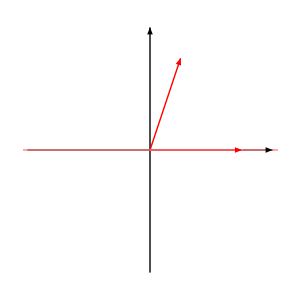

```mathematica
A={{3, 1}, {0, 3}};
Graphics[{Arrow[4{{{-1,0},{1,0}},{{0,-1},{0,1}}}],Red,Arrow[{{{0,0},A⟦All,1⟧},{{0,0},A⟦All,2⟧}}],White, Arrow[{{A⟦All,1⟧,{4,3}},{A⟦All,2⟧,{4,3}}}],Pink,InfiniteLine[{{0,0},{1,0}}]},ImageSize->300]
```

Diagonalization and Powers of A

#### Suppose A has n independent eigenvectors: x_1,x_2,...,x_n A S=A [x_1 | x_2 | ... | x_n]=[λ_1 x_1 | λ_2 x_2 | ... | λ_n x_n]=[x_1 | x_2 | ... | x_n](λ_1 | 0 | ... | 0 0 | λ_2 | ... | 0 ... | ... | ... | ... 0 | 0 | ... | λ_n)=S Λ→A=S Λ S^-1 If A x = λ x, then A(A x) = λ A (x)→A^2 x=λ^2 x If A = S Λ S^-1, then A^2 = S Λ S^-1 S Λ S^-1=S Λ^2 S^-1 If λ_i≠ λ_j ∀ i≠j ⇒ its eigenvectors are independent. Let u_(k+1)=A u_k→u_k=A^k u_0 We express u_0 in terms of eigenvectors: u_0=c_1 x_1+c_2 x_2+... c_n x_n=S c So it becomes S Λ^k c, which can be easily computed Example with Fibonacci: F_(k+2)=F_(k+1)+F_k Trick: Let u_k=(F_(k+1) F_k), then u_(k+1)=(F_(k+2) F_(k+1))=(1 | 1 1 | 0)(F_(k+1) F_k)=(1 | 1 1 | 0)u_k=A u_k det(A-λ I)=λ^2-λ-1=0→λ_1=φ,λ_2=-Φ u_0=(F_1 F_0)=(1 0) ⋆ φ=(1+√5)/2=1/Φ,Φ=(√5-1)/2=1/φ ⋆ φ-Φ=1=φ Φ ⋆ φ^2=φ+1 ⋆ Φ^2+Φ=1 For λ_1=φ: (1-φ | 1 1 | -φ)(φ 1)=(φ-φ^2+1 φ-φ)=(0 0) For λ_2=-Φ: (1+Φ | 1 1 | Φ)(-Φ 1)=(Φ^2+Φ-1 Φ-Φ)=(0 0) Ought to find c_1,c_2 such that: (φ | -Φ 1 | 1)(c_1 c_2)=(1 0)←u_0 c_1=1/(φ+Φ) c_2=-1/(φ+Φ) (F_(k+1) F_k)=(φ | -Φ 1 | 1)(φ | 0 0 | -Φ)^k(1/(√5) -1/(√5)) Actually, it’s shifted forward by 1...? F_1=1

```mathematica
DynamicModule[{k=100},Dynamic@Row[{Style["F(",25],Style[InputField[Dynamic[k],FieldSize->1.7],15],
Dynamic[Style[StringForm[")=``",(Round@@@(({{(1+√5)/2, (1-√5)/2}, {1, 1}}).(({{(1+√5)/2, 0}, {0, (1-√5)/2}})^(k-1)).({{1/(√5)}, {-1/(√5)}})))⟦2⟧],25]]}]]
```

Differential Equations and exp(At)

#### Example: u_0=[1 0] du/dt=d/dt[u_1 u_2]={du_1/dt=-u_1+2 u_2 du_2/dt= u_1- 2 u_2=[-1 | 2 1 | -2][u_1 u_2]=A u λ_1 = 0: x_1=[2 1]→A x_1= 0 x_1 λ_2 = -3: x_2=[1 -1]→A x_2= -3 x_1 Solution:du/dt=Au, u=e^(λ_1 t)x_1 λ_1 e^(λ_1 t)x_1=A e^(λ_1 t)x_1→λ_1 x_1=A x_1 u(t)=c_1 e^(λ_1 t)x_1+c_2 e^(λ_2 t)x_2 Compare with: u_(k+1)=A u_k→c_1 λ_1^k x_1+c_2 λ_2^k x_2 Finding c_1 and c_2: u(0)=[1 0]=c_1[2 1]+c_2[1 -1] →c_1=c_2=1/3 Full answer: u(t)=1/3[2 1]+1/3[1 -1]e^(-3t) Steady state: lim t→∞ u(t)=1/3[2 1] For stability (lim t→∞ u(t)=0), we need Re( λ )<0∀λ. Since ||e^(ⅈ y)||=1 ⇒||e^(x + ⅈ y)||=||e^x|| For steady state (lim t→∞ u(t)=c), we need at least one λ=0 and Re( λ )<0 for the rest. For blow-up (lim t→∞ u(t)=∞), we need at least one Re( λ )>0 Writing the solution in terms of eigenvalues: du/dt=Au, Set u=S v where S is the matrix of eigenvectors S dv/dt=A S v→dv/dt=S^-1 A S v=Λ v When using eigenvectors as basis, the equations get “uncoupled”: dv_i/dt=λ_i v_i ∀i v(t)=e^(Λ t)v(0) u(t)=e^(A t) u(0)=S e^(Λ t)S^-1 u(0) From the power series: e^(A t)=I +A t + (A t)^2/2+...=I+[S Λ S^-1]t+(([S Λ S^-1]t)^2)/2+...=S S^-1+S Λ S^-1 t+(S Λ^2 S^-1 t^2)/2+...=S e^(Λ t)S^-1 e^(Λ t)=(e^(λ_1 t) | 0 | ... | 0 0 | e^(λ_2 t) | ... | 0 ... | ... | ... | ... 0 | 0 | ... | e^(λ_n t)) *From the geometric series: (I-A t)^-1≈I+A t + (A t)^2, for small t’s Example: y'' +b y' + k y=0 2^nd order equation → 2×2 , 1^st order system: u=[y' y]→u'=[y'' y']=[-b y'-ky y']=[-b | -k 1 | 0][y' y]

Markov Matrices; Fourier Series

#### Markov matrix: A=(.1 | .01 | .3 .2 | .99 | .3 .7 | .0 | .4) Related to probabilities, therefore: Only positive reals and columns add up to one. Every Markov matrix has λ_1 = 1 and ||λ_i||≤ 1 for every other eigenvalue. x_1≥ 0 in every entry x_1 ends up being the steady-state Since 1 is an eigenvalue, A - I must be singular. A - I=(-.9 | .01 | .3 .2 | -.01 | .3 .7 | 0 | -.6) Every column adds up to zero ⇔ (1 | 1 | 1)∈N(Aᵀ) det(A) = det(Aᵀ) ⇒ eigenvalues(A) =eigenvalues(Aᵀ) x_1=(.6 33 .7) Application: u_(k + 1) = A u_k, where A is a Markov matrix We can model, for example, population migration (u_cal u_mass)_0=(0 1000) (u_cal u_mass)_(k+1)=(.9 | .2 .1 | .8)(u_cal u_mass)_k λ_1=1: (-.1 | .2 .1 | -.2)→x_1=(2 1) λ_2=.7 (.2 | .2 .1 | .1)→x_2=(-1 1) u_k= c_1(2 1) + (c_2(.7))^k(-1 1) u_k= 1000/3(2 1) + 2000/3(.7)^k(-1 1)

```mathematica
u0 = {{0},{1000}};
A = {{.9,.2},{.1,.8}};
uk[A_,u0_,t_]:=(
eigval = Eigenvalues[A];
eigvec = Eigenvectors[A]ᵀ;
c = RowReduce@Join[eigvec,u0,2];
c1 = c⟦1,3⟧;c2=c⟦2,3⟧;
x1 = eigvec⟦All,1⟧;x2=eigvec⟦All,2⟧;
c1*eigval⟦1⟧^t*x1+c2*eigval⟦2⟧^t*x2
)
ListLinePlot[{Table[uk[A,u0,t]⟦1⟧,{t,0,20}],Table[uk[A,u0,t]⟦2⟧,{t,0,20}]},InterpolationOrder->10,AxesLabel->{"time","population"},PlotLabels->{"u_cal","u_mass"}]
```

-Graphics-

#### Given an orthonormal basis Q = {q_1,q_2,...,q_n}, and a vector v: v=c_1 q_1+c_2 q_2+...+c_n q_n Since q_i ᵀ q_j={1, i=j 0, i ≠j c_1=q_1 ᵀv In matrix form: v=(q_1 | q_2 | ... | q_n)(c_1 c_2 ... c_n)=Q C Since Q has orthonormal columns, Q^-1=Qᵀ⇒C=Qᵀv Instead of working in an n-dimensional vector space, we can work in an infinite-dimensional function space: For fourier series, f(x) is orthogonal to g(x) if (∫_0)^(2π) f(x) g(x)dx=0 f(x)=a_0+a_1 cos (x)+b_1 sin(x)+a_2 cos (2x)+b_2 sin(2x)+... (∫_0)^(2π)f(x)cos(x)=(∫_0)^(2π) a_1 cos^2(x)⇒a_1=1/π(∫_0)^(2π)f(x)cos(x)

Symmetric Matrices and Positive Definiteness

#### Symmetric matrices always have: ⋆ Real eigenvalues ⋆ Perpendicular eigenvectors SPECTRAL THEOREM: If A is symmetric we can decompose it as: A=Q Λ Qᵀ=λ_1 q_1 q_1 ᵀ+λ_2 q_2 q_2 ᵀ+..., where Q is an orthogonal matrix. A x = λ x ⇒{x^—ᵀA^—ᵀ = x^—ᵀ λ^—⇒x^—ᵀA^—ᵀx = x^—ᵀ λ^—x x^—ᵀA x = x^—ᵀλ x Since x^—ᵀA x≠0 , if A^—ᵀ=A⇒λ = λ^—⇒ λ∈ ℝ #pivots > 0 = #eigenvalues > 0 ?????? A positive definite matrix is a symmetric matrix whose eigenvalues, pivots, determinant and sub-determinants are all positive

Complex Matrices; Fast Fourier Transform

#### Let Z ∈ ℂ^n, then ||z_1(||)^2+||z_2(||)^2+...=Z^—ᵀZ=Z^*Z=Z^H Z H stands for Hermitian. Let A ∈ ℂ^n, then A is Hermitian (symmetric) if A^H=A If A^H=A, then λ_1,...,λ_n∈ ℝ, and x_i^H x_j={0, i≠j 1,i=j If Q^H Q=I , then Q is said to be unitary ·Fast Fourier Transform F_n=(1 | 1 | 1 | ... | 1 1 | w | w^2 | ... | w^(n-1) 1 | w^2 | w^4 | ... | w^(2(n-1)) ... | ... | ... | ... | ... 1 | w^(n-1) | w^(2(n-1)) | ... | w^((n-1)^2))=w^(i j), where w is the nth root of unity (w_n=ⅇ^(ⅈ (2π)/n)) The columns of F_n are always orthogonal Let n = 4, then F_4=(1 | 1 | 1 | 1 1 | i | i^2 | i^3 1 | i^2 | i^4 | i^6 1 | i^3 | i^6 | i^9)=(1 | 1 | 1 | 1 1 | i | -1 | -i 1 | -1 | 1 | -1 1 | -i | -1 | i) Normalizing: F_4=1/2(1 | 1 | 1 | 1 1 | i | -1 | -i 1 | -1 | 1 | -1 1 | -i | -1 | i) Then, F_4^H F_4=I Note that (w_64)^2=w_32 Then we can factor F_n into [I | D I | -D][F_(n/2) | 0 0 | F_(n/2)][P], where: P is a permutation matrix that separates odd and even D is diag (1, w, w^2,... w^(n-1)) We can further factorize F_(n/2) and so on, reducing the operational cost from n^2 to n/2 log_2 n For example: F_4=(1 | 1 | 1 | 1 1 | i | -1 | -i 1 | -1 | 1 | -1 1 | -i | -1 | i)=(1 | 0 | 1 | 0 0 | 1 | 0 | w 1 | 0 | -1 | 0 0 | 1 | 0 | -w)(1 | 1 | 0 | 0 1 | -1 | 0 | 0 0 | 0 | 1 | 1 0 | 0 | 1 | -1)(1 | 0 | 0 | 0 0 | 0 | 1 | 0 0 | 1 | 0 | 0 0 | 0 | 0 | 1)

Positive Definite Matrices and Minima

#### Tests for 2×2: ·(eigenvalues)λ_1>0,λ_2>0 ·(determinants) a>0,a c -b^2>0 ·(pivots) a>0,(a c -b^2)/a>0 ·xᵀA x=(x_1 | x_2)(a | b c | d)(x_1 x_2)=a x_1^2+(b+c)x_1 x_2+d x_2^2=(a(x_1+((b + c)/(2 a))x_2))^2+(d-((b + c)/(2 a))^2)x_2^2 We can connect this to Gaussian elimination: A=L U ⇒(a | b c | d) =(1 | 0 (b + c)/(2 a) | 1)(a | b 0 | d-((b + c)/(2 a))^2)

```mathematica
A = ({{2, 6}, {6, 19}});
a=A⟦1,1⟧;b=A⟦1,2⟧;c=A⟦2,1⟧;d=A⟦2,2⟧;
Show[{
Graphics3D[InfinitePlane[{{1,0,0},{0,1,0},{0,0,0}}],ImageSize->200,SphericalRegion->True],
Plot3D[a x^2+(b+c)x y+d y^2,{x,-5,5},{y,-5,5},PlotRange->d,MeshStyle->None]}]
```

-Graphics3D-

#### We identify a minimum in an n-dimensional system by nothing if its matrix of 2^nd derivatives is positive definite. For 2×2:xᵀ(f_xx | f_xy f_yx | f_yy)x>0 3×3 example: xᵀA x=xᵀ(a | b | c d | e | f g | h | i)x=a x_1^2+(b+d)x_1 x_2+e x_2^2+(c+g)x_1 x_3+i x_3^2+(f+h)x_2 x_3 for f = 1

```mathematica
A = ({{2, -1, 0}, {-1, 2, -1}, {0, -1, 2}});
a = A⟦1,1⟧;b = A⟦1,2⟧;c = A⟦1,3⟧;d = A⟦2,1⟧;e = A⟦2,2⟧;f = A⟦2,3⟧;g = A⟦3,1⟧;h = A⟦3,2⟧;i = A⟦3,3⟧;
ax = Eigenvectors@A;
len = Eigenvalues@A;
Show[{ContourPlot3D[a x^2+(b+d)x y + e y^2+(c+g)x z +i z^2+(f+h)y z==1,{x,-1,1},{y,-1,1},{z,-1,1},MeshStyle->None,SphericalRegion-> True,ContourStyle->Directive[Opacity[0.3],Black],ImageSize->400],
Graphics3D[{White,Line[{{{0,0,0},ax⟦1⟧/len⟦1⟧},{{0,0,0},ax⟦2⟧/len⟦2⟧},{{0,0,0},ax⟦3⟧/len⟦3⟧}}],Red,Point[{ax⟦1⟧/len⟦1⟧,ax⟦2⟧/len⟦2⟧,ax⟦3⟧/len⟦3⟧}]}]}]
```

-Graphics3D-

#### The direction of the axis are given by the eigenvectors ??? The half-length of the axis are given by the inverse of the eigenvalues PRINCIPAL AXIS THEOREM A=Q Λ Qᵀ

Similar Matrices and Jordan Form

#### If A and B are positive definite, then A+B is positive definite. Let A be any m×n matrix, then: AᵀA is always positive definite since xᵀAᵀAx=(A x)ᵀA x=||A x(||)^2≥0 For positive definite matrices you never need to do row exchanges (???) Let A and B be n×n matrices, then: A and B are said to be similar if there exist a matrix M such that: B=M^-1 A M For example: A is similar to Λ since: S^-1 A S=Λ Suppose A=(2 | 1 1 | 2), Then, λ_1=3, λ_2=1 Suppose M = (1 | 4 0 | 1) Then B=(1 | -4 0 | 1)(2 | 1 1 | 2)(1 | 4 0 | 1)=(-2 | -15 1 | 6), which also has λ_1=3, λ_2=1 Theorem: Similar matrices have the same eigenvalues Proof: A x = λ x⇒M^-1 A [M M^-1]x=M^-1 λ x⇒B [M^-1 x]=λ [M^-1 x] Corollary: The eigenvector of B is M^-1 x The eigenvectors of a diagonal matrix are always: [1 0] & [0 1] Suppose A_1=(4 | 0 0 | 4), with λ_1=λ_2=4 Suppose A_2=(4 | 1 0 | 4), then λ_1=λ_2=4 But, M^-1(4 | 0 0 | 4)M=4M^-1(1 | 0 0 | 1)M=(4 | 0 0 | 4) Then we have two disjoint families of similar 2×2 matrices with repeated eigenvalue 4. We can see A_2 is not diagonalizable since it’s not similar to A_1 and therefore it has only one eigenvector. A_2 is what is called a Jordan normal/canonical form (JCF), which has a 1 above the main diagonal for every dimension of the nullspace We ought to differentiate (0 | 1 | 0 | 0 0 | 0 | 1 | 0 0 | 0 | 0 | 0 0 | 0 | 0 | 0) from (0 | 1 | 0 | 0 0 | 0 | 0 | 0 0 | 0 | 0 | 1 0 | 0 | 0 | 0) through their Jordan blocks Jordan blocks have the form: J_i=(λ_i | 1 | 0 | ... | 0 0 | λ_i | 1 | ... | 0 0 | 0 | λ_i | ... | 0 ... | ... | ... | ... | ... 0 | 0 | 0 | λ_i | 1 0 | 0 | 0 | ... | λ_1), and have a single eigenvector Every square matrix A is similar to a Jordan matrix J: J=(J_1 | 0 | ... | 0 0 | J_2 | ... | 0 ... | ... | ... | ... 0 | 0 | ... | J_d), where d is the number of eigenvectors of A If A has n distinct eigenvectors, then J = Λ

Singular Value Decomposition

#### A = U Σ Vᵀ If A is positive definite, then A = Q Λ Qᵀ, where Q is an orthogonal matrix We look for an orthogonal basis {v_1,v_2,...,v_n} in C(Aᵀ) that is also orthogonal in C(A) {σ_1 u_1,σ_2 u_2,...,σ_r u_r}, where u_1=A v_1 A [v_1 | v_2 | ... | v_r]=[u_1 | u_2 | ... | u_r](σ_1 | 0 | ... | 0 0 | σ_2 | ... | 0 ... | ... | ... | 0 0 | 0 | 0 | σ_r)⇒A V = U Σ⇒A=U Σ V^-1=U Σ Vᵀ Then AᵀA=(V Σ ᵀUᵀ)(U Σ Vᵀ)=V (σ_1^2 | 0 | ... | 0 0 | σ_1^2 | ... | 0 ... | ... | ... | ... 0 | 0 | ... | σ_r^2)Vᵀ Example: A=(4 | 4 -3 | 4) Aᵀ A=(4 | -3 4 | 4)(4 | 4 -3 | 4)=(25 | 7 7 | 25) Eigenvectors ⇒ V Eigenvalues ⇒ σ^2 λ_1=32 x_1=1/(√2)(1 1) λ_2=18 x_2=1/(√2)(1 -1) Σ=(√32 | 0 0 | √18) V=1/(√2)(1 | 1 1 | -1) To find U: A Aᵀ=U Σ Σᵀ Uᵀ Luckily, A Aᵀ=(32 | 0 0 | 18) And therefore U=(1 | 0 0 | 1) Somewhere we messed up To find U: C V = U Σ Example #2 (Singular): A =(4 | 3 8 | 6) v_1 =(.8 .6) (Row Space) v_2 =(.6 -.8) N(A) V=(.8 | .6 .6 | -.8)=Vᵀ u_1 =1/(√5)(1 2) (Column Space) u_2 =1/(√5)(2 -1) N(Aᵀ) U=1/(√5)(1 | 2 2 | -1)

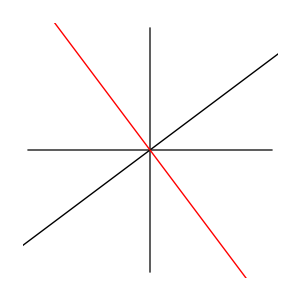
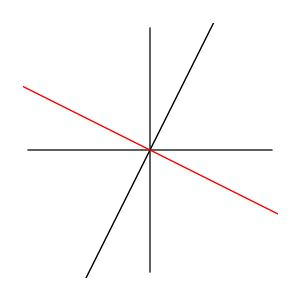
Row Space
-Graphics-Column Space
-Graphics-Row/Column Spaces
Nullspaces

```mathematica
Row[{
Column[{
Style["Row Space",40],
Graphics[{GrayLevel[.1],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}],Black,Thick,InfiniteLine[{{0,0},{4,3}}],Red,InfiniteLine[{{0,0},{1,-4/3}}]},ImageSize->300]
},Center],
Column[{
Style["Column Space",40],
Graphics[{GrayLevel[.1],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}],Black,Thick,InfiniteLine[{{0,0},{4,8}}],Red,InfiniteLine[{{0,0},{1,-1/2}}]},ImageSize->300]
},Center],
Column[{
Style["Row/Column Spaces",Black,20],
Style["Nullspaces",Red,20]
},Center]
}]
```

#### AᵀA =(80 | 60 60 | 45)⇒λ_1=0,λ_2=125⇒Σ=(√125 | 0 0 | 0) A =U Σ Vᵀ=1/(√5)(1 | 2 2 | -1)(√125 | 0 0 | 0)(.8 | .6 .6 | -.8) A v_i=σ_i u_i We are choosing the right basis for the four subspaces: v_1,...,v_r is an orthonormal basis for the row space u_1,...,u_r is an orthonormal basis for the column space v_(r+1),...,v_n is an orthonormal basis for N(A) u_(r+1),...,u_m is an orthonormal basis for N(Aᵀ)

Linear Transformations and Their Matrices

#### Linear Transformations lead to matrices when we introduce a coordinate system Linearity formally means: ·T(v+w)=T(v)+T(w) ·T(c v)=c T(v) A linear transformation will always map the origin to the origin Example: ·Projection to a line in ℝ^2 ·Rotation

```mathematica
rot[t_]:= ({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}});
trans[T_,v_]:=Flatten[{v,v.T},1]
Manipulate[{
Graphics[Table[Arrow[trans[rot[θ],({{x, y}})]],{x,-3,3},{y,-3,3}]]},{{θ,0},-2π,2π,π/10}
]
```

#### Every matrix A defines a linear transformation by T(v) = A v Given what a transformation does to a basis, we can know what it does to every vector since they can be decomposed in that basis. Input and output basis may be different For example, for projection to a line in ℝ^2: Taking the eigenvectors v_1 and v_2 as basis: Any vector v can be expressed as: v=c_1 v_1+c_2 v_2

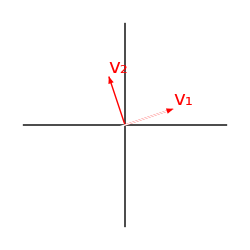

```mathematica
Graphics[{Line[2{{-1,0},{1,0}}],Line[2{{0,-1},{0,1}}],White,InfiniteLine[{{0,0},{3,1}}],Red, Arrow[{{0,0},Normalize@{3,1}}],Arrow[{{0,0},Normalize@{-1,3}}],Inset[Style["v_1",20],Normalize@{3,1},{Left,Bottom}],Inset[Style["v_2",20],Normalize@{-1,3},{Left,Bottom}]},ImageSize->250]
```

#### We observe a projection to the line only keeps the component in the v_1 direction, therefore the matrix A that describes the transformation is: A=(1 | 0 0 | 0) Which is Λ since we chose an eigen-basis Generally, to find A: Given an input basis {v_(1,)... v_n} and an output basis {w_1,...,w_m} A=(a_11 | a_12 | ... | a_(1n) a_21 | a_22 | ... | a_(2n) ... | ... | ... | ... a_m1 | a_m2 | ... | a_mn) Where T(v_k)=a_(1k)w_1+a_(2k)w_2+...+a_mk w_m Example: T=d/dx Input : c_1+c_2 x+c_3 x^2; basis: 1,x,x^2 Output : c_2+2 c_3 x; basis: 1,x A (c_1 c_2 c_3)=(c_2 2 c_3)⇒A = (0 | 1 | 0 0 | 0 | 2)

Change of Basis; Image Compression

#### Pixels in an image are highly correlated with nearby pixels. In a video, frames are also highly correlated. With a smart change of basis we can have lossless compression. JPEG uses the Fourier basis which is based off the Fourier matrix. Lossy compression occurs when we set a cutoff to get rid of the small coefficients Wavelet basis goes as follows: {(1 1 1 1 1 1 1 1),(1 1 1 1 -1 -1 -1 -1),(1 1 -1 -1 0 0 0 0),(0 0 0 0 1 1 -1 -1),(1 -1 0 0 0 0 0 0),(0 0 1 -1 0 0 0 0),(0 0 0 0 1 -1 0 0),(0 0 0 0 0 0 1 -1)} Given a signal P and a basis W, to find the coefficients C we simply solve: C = W^-1 P Therefore a good basis must have an inverse that is easily computable For the Fourier basis, we use FFT to do the change of basis For the wavelet basis, since it’s orthogonal we can normalize and W^-1=Wᵀ Given a transformation T: Let A be its matrix with respect to a basis V Let B be its matrix with respect to a basis W Then ∃M∍B=M^-1 A M If we have an eigen-basis then the matrix A of coefficients becomes Λ, but since finding eigenvalues is computationally expensive we use other basis.

Left and Right Inverse; Pseudoinverse

#### 2-sided inverses Occurs when a matrix has full rank and is square (r=m=n) Left-inverses Occurs when a matrix has full column rank (r=n<m) N(A)={0} with 1 or 0 solutions to A x=b dim(N(Aᵀ))=m-r AᵀA has the same rank as A Since AᵀA is n×n, A Aᵀ is full rank (AᵀA)^-1 then exists and we can define the left inverse of A: [(AᵀA)^-1 Aᵀ ]A=I A [(AᵀA)^-1 Aᵀ ] : projects A into the column space Right-inverses Occurs when a matrix has full row rank (r=m<n) N(Aᵀ)={0} with ∞ solutions to A x=b dim(N(A))=n-r A Aᵀ has the same rank as A Since AᵀA is m×m, A Aᵀ is full rank (A Aᵀ)^-1 then exists and we can define the right inverse of A: A [Aᵀ(A Aᵀ)^-1]=I [Aᵀ(A Aᵀ)^-1]A: projects A into the row space Pseudo-inverse If we restrict ourselves to only x’s in the row space We have that A: C(Aᵀ) → C(A) is a bijection We can therefore define the pseudo inverse A^+: C(A) → C(Aᵀ) Proof: Let {x, y} ∈ C(Aᵀ) with x≠y Since it’s a vector space {x – y} ∈ C(Aᵀ) Suppose A x=A y⇒A(x-y)=0 Then x-y∈N(A) →← Very useful for least squares. To find the pseudoinverse A^+: From SVD: A=U Σ Vᵀ We can easily invert U and Vᵀ since they are orthonormal so we only need to worry about Σ But since Σ=(σ_1 | 0 | ... | 0 | ... 0 | σ_2 | ... | 0 | ... ... | ... | ... | 0 | ... 0 | 0 | 0 | σ_r | ... ... | ... | ... | ... | ...) m×n Σ^+=(1/σ_1 | 0 | ... | 0 | ... 0 | 1/σ_2 | ... | 0 | ... ... | ... | ... | 0 | ... 0 | 0 | 0 | 1/σ_r | ... ... | ... | ... | ... | ...) n×m Then Σ Σ^+=(1 | 0 | ... | 0 | ... 0 | 1 | ... | 0 | ... ... | ... | ... | 0 | ... 0 | 0 | 0 | 1 | ... ... | ... | ... | ... | ...) m×m And Σ^+Σ=(1 | 0 | ... | 0 | ... 0 | 1 | ... | 0 | ... ... | ... | ... | 0 | ... 0 | 0 | 0 | 1 | ... ... | ... | ... | ... | ...) n×n Finally we’ve got A^+=V Σ^+Uᵀ